```mathematica
Name:Nehel Siddiqui
Father Name: Gulzar Ahmed Siddiqui 
Seat number:H1516136 
Program :Milne's method
 Submitted tO:Ma'am Samreen
```

```mathematica
"dy/dx =2e^x-y ,y(0)=2 ,y(0.1)=2.010 ,y(0.2)=2.04 ,y(0.3)=2.09 Find y(o.4)=?by milne's predictor and corrector formula" ;
```

```mathematica
Clear ["Global`"]
```

```mathematica
"f(x,y)=y'[x]"
```

f(x,y)=y'[x]

```mathematica
f[x_,y_]=2 Exp [x]-y
```

2 ⅇ^x-y

```mathematica
{y[0]=2 , y[1]=2.010, y[2]=2.040, y[3]=2.090, x[0]=0,x[1]=0.1,x[2]=0.2,x[3]=0.3, h=0.1}
```

{2,2.01,2.04,2.09,0,0.1,0.2,0.3,0.1}

```mathematica
a=Do[  y'[n-3]=f[x[n-3],y[n-3]] ;  y'[n-2]=f[x[n-2],y[n-2]];  y'[n-1]=f[x[n-1],y[n-1]];  y'[n]=f[x[n],y[n]]; x[n+1];Print[y[n+1,P]=y[n-3]+4 h (2 y'[n-2] - y'[n-1] + 2 y'[n]) /3 //N] ;x[n+1]=x[n]+h ;[y[n+1]=y[n+1,P]];  y'[n+1,P]=f[x[n+1],y[n+1]],  {n,3 ,8}]
```

2.16231

2.25514

2.37103

2.50957

2.67527

2.86582

```mathematica
{y[0,C]=2, y[1,C]=2.010, y[2,C]=2.040, y[3,C]=2.090, x[0]=0,x[1]=0.1,x[2]=0.2,x[3]=0.3, h=0.1}
```

{2,2.01,2.04,2.09,0,0.1,0.2,0.3,0.1}

```mathematica
Do[ h=0.1;  y'[n-3]=f[x[n-3]] ;  y'[n-2]=f[x[n-2],y[n-2]];  y'[n-1]=f[x[n-1],y[n-1]];  y'[n]=f[x[n],y[n]]; Print[x[n+1]];   Print[y[n+1,C]=y[n-1]+ h (y'[n-1]  +4 y'[n] +y'[n+1,P]) /3 //N] ;x[n+1]=x[n]+h ;y[n+1]=y[n+1,P]; [ y'[n+1,C]=f'[x[n+1],y[n+1]]],  {n, 3,8}]
```

0.4

2.1621

0.5

2.25458

0.6

2.3711

0.7

2.51025

0.8

2.67505

0.9

2.86539

```mathematica
iterations=Table[n,{n,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
X=Table [ x[n+1]  //N, {n,-1,8}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}

```mathematica
Corrector=Table [y[n+1,C] //N ,{n, -1,8}]
```

{2.,2.01,2.04,2.09,2.1621,2.25458,2.3711,2.51025,2.67505,2.86539}

```mathematica
Clear[x,y]
```

```mathematica
A=DSolve[{y'[x]==2  Exp[x]-y[x],y[0]==2},y[x],x]
```

{{y[x]→ⅇ^-x (1+ⅇ^(2 x))}}

```mathematica
exact=Table[ⅇ^-x (1+ⅇ^(2 x)),{x,0,0.9,0.1}]
```

{2.,2.01001,2.04013,2.09068,2.16214,2.25525,2.37093,2.51034,2.67487,2.86617}

```mathematica
tab1=Table[{iterations[[n]],X[[n]],Corrector[[n]],exact[[n]],ScientificForm[Abs[Corrector[[n]]-exact[[n]]]]},{n,1,10}]
```

{{0,0.,2.,2.,0.},{1,0.1,2.01,2.01001,8.33611×10^-6},{2,0.2,2.04,2.04013,1.33511×10^-4},{3,0.3,2.09,2.09068,6.77028×10^-4},{4,0.4,2.1621,2.16214,4.41797×10^-5},{5,0.5,2.25458,2.25525,6.72578×10^-4},{6,0.6,2.3711,2.37093,1.69666×10^-4},{7,0.7,2.51025,2.51034,9.20357×10^-5},{8,0.8,2.67505,2.67487,1.80578×10^-4},{9,0.9,2.86539,2.86617,7.80537×10^-4}}

```mathematica
tab2=Prepend[ tab1,{"iterations","X","Corrector","exact","Error"}]
```

{{iterations,X,Corrector,exact,Error},{0,0.,2.,2.,0.},{1,0.1,2.01,2.01001,8.33611×10^-6},{2,0.2,2.04,2.04013,1.33511×10^-4},{3,0.3,2.09,2.09068,6.77028×10^-4},{4,0.4,2.1621,2.16214,4.41797×10^-5},{5,0.5,2.25458,2.25525,6.72578×10^-4},{6,0.6,2.3711,2.37093,1.69666×10^-4},{7,0.7,2.51025,2.51034,9.20357×10^-5},{8,0.8,2.67505,2.67487,1.80578×10^-4},{9,0.9,2.86539,2.86617,7.80537×10^-4}}

```mathematica
Grid[tab2,Frame->All,Spacings->{1, 1}]
```

iterations | X | Corrector | exact | Error
0 | 0. | 2. | 2. | 0.
1 | 0.1 | 2.01 | 2.01001 | 8.33611×10^-6
2 | 0.2 | 2.04 | 2.04013 | 1.33511×10^-4
3 | 0.3 | 2.09 | 2.09068 | 6.77028×10^-4
4 | 0.4 | 2.1621 | 2.16214 | 4.41797×10^-5
5 | 0.5 | 2.25458 | 2.25525 | 6.72578×10^-4
6 | 0.6 | 2.3711 | 2.37093 | 1.69666×10^-4
7 | 0.7 | 2.51025 | 2.51034 | 9.20357×10^-5
8 | 0.8 | 2.67505 | 2.67487 | 1.80578×10^-4
9 | 0.9 | 2.86539 | 2.86617 | 7.80537×10^-4

```mathematica
Corrector={{0,2},{0.1,2.01},{0.2,2.04},{0.3,2.09},{0.4,2.1621},{0.5,2.25458},{0.6,2.3711},{0.7,2.51025},{0.8,2.67505},{0.9,2.86539}}
```

{{0,2},{0.1,2.01},{0.2,2.04},{0.3,2.09},{0.4,2.1621},{0.5,2.25458},{0.6,2.3711},{0.7,2.51025},{0.8,2.67505},{0.9,2.86539}}

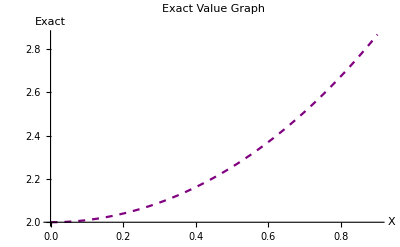

```mathematica
P1=Plot[Exp[x]+Exp[-x]//N ,{x, 0,0.9},PlotRange->Full,PlotStyle->{Dashed,Purple},AxesLabel->{"X","Exact "}, PlotLabel->"Exact Value Graph",LabelStyle->{Black,19,Bold,Italic}]
```

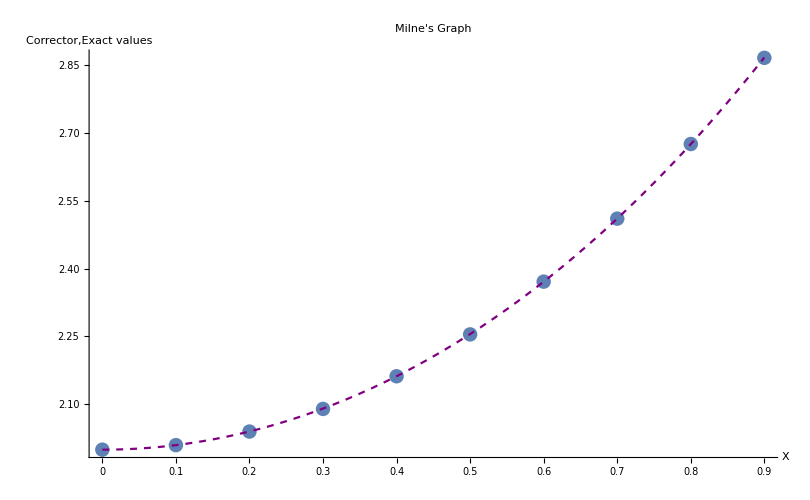

```mathematica
m1=Show[ListPlot[Corrector], P1,PlotLabel->"Milne's Graph",AxesLabel->{"X","Corrector,Exact values"},LabelStyle->{Black,20,Bold},Ticks->{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},Automatic}]
```

```mathematica
"NOTE :Here Dots shows corrector values, dashed shows Exact values";
```

```mathematica
"EXAMPLE NUMBER 2";
```

```mathematica
"dy/dx =(x+y)/2 ,y(0)=2 ,y(0.5)=2.636 ,y(1)=3.595 ,y(1.5)=4.968 Find y(2)=?and perform iteration for 5 more values by milne's predictor and corrector formula" ;
```

```mathematica
Clear ["Global`"]
```

```mathematica
"y'[x]=f[x,y]";
```

```mathematica
f[x_,y_]=(x+y)/2
```

(x+y)/2

```mathematica
{y[0]=2 , y[1]=2.636, y[2]=3.595, y[3]=4.968, x[0]=0,x[1]=0.5,x[2]=1,x[3]=1.5, h=0.5}
```

{2,2.636,3.595,4.968,0,0.5,1,1.5,0.5}

```mathematica
Do[ y'[n-3]=f[x[n-3],y[n-3]] ;  y'[n-2]=f[x[n-2],y[n-2]];  y'[n-1]=f[x[n-1],y[n-1]];  y'[n]=f[x[n],y[n]]; x[n+1];Print[y[n+1,P]=y[n-3]+4 h (2 y'[n-2] - y'[n-1] + 2 y'[n]) /3 //N] ;x[n+1]=x[n]+h ;[y[n+1]=y[n+1,P]];  y'[n+1,P]=f[x[n+1],y[n+1]],  {n, 3,8}]
```

6.871

9.45733

12.9216

17.5106

23.5424

31.4298

```mathematica
{y[0,C]=2 , y[1,C]=2.636, y[2,C]=3.595, y[3,C]=4.968, x[0]=0,x[1]=0.5,x[2]=1,x[3]=1.5, h=0.5}
```

{2,2.636,3.595,4.968,0,0.5,1,1.5,0.5}

```mathematica
Do[   y'[n-3]=f[x[n-3],y[n-3]] ;  y'[n-2]=f[x[n-2],y[n-2]];  y'[n-1]=f[x[n-1],y[n-1]];  y'[n]=f[x[n],y[n]]; Print[x[n+1]];Print[y[n+1,C]=y[n-1]+ h (y'[n-1]  +4 y'[n] +y'[n+1,P]) /3 //N] ;x[n+1]=x[n]+h ;y[n+1]=y[n+1,P]; [ y'[n+1,C]=f[x[n+1],y[n+1]]],  {n, 3,8}]
```

2.

6.87317

2.5

9.46044

3.

12.9228

3.5

17.5118

4.

23.5471

4.5

31.4364

```mathematica
iterations=Table[n,{n,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
X=Table [ x[n+1]  //N, {n,-1,8}]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5}

```mathematica
Corrector=Table [y[n+1,C] //N ,{n, -1,8}]
```

{2.,2.636,3.595,4.968,6.87317,9.46044,12.9228,17.5118,23.5471,31.4364}

```mathematica
Clear[x,y]
```

```mathematica
A=DSolve[{y'[x]==(x+y[x])/2,y[0]==2},y[x],x]
```

{{y[x]→-2+4 ⅇ^(x/2)-x}}

```mathematica
Exact=Table[-2+4 ⅇ^(x/2)-x,{x,0,4.5,0.5}]
```

{2.,2.6361,3.59489,4.968,6.87313,9.46137,12.9268,17.5184,23.5562,31.4509}

```mathematica
Tab1=Table[{iterations[[n]],X[[n]],Corrector[[n]],Exact[[n]],ScientificForm[Abs[Corrector[[n]]-Exact[[n]]]]},{n,1,10}]
```

{{0,0.,2.,2.,0.},{1,0.5,2.636,2.6361,1.01667×10^-4},{2,1.,3.595,3.59489,1.14917×10^-4},{3,1.5,4.968,4.968,6.64507×10^-8},{4,2.,6.87317,6.87313,3.93528×10^-5},{5,2.5,9.46044,9.46137,9.27385×10^-4},{6,3.,12.9228,12.9268,3.93221×10^-3},{7,3.5,17.5118,17.5184,6.56503×10^-3},{8,4.,23.5471,23.5562,9.139×10^-3},{9,4.5,31.4364,31.4509,1.45078×10^-2}}

```mathematica
Tab2=Prepend[ Tab1,{"iterations","X","Corrector","Exact","Error"}]
```

{{iterations,X,Corrector,Exact,Error},{0,0.,2.,2.,0.},{1,0.5,2.636,2.6361,1.01667×10^-4},{2,1.,3.595,3.59489,1.14917×10^-4},{3,1.5,4.968,4.968,6.64507×10^-8},{4,2.,6.87317,6.87313,3.93528×10^-5},{5,2.5,9.46044,9.46137,9.27385×10^-4},{6,3.,12.9228,12.9268,3.93221×10^-3},{7,3.5,17.5118,17.5184,6.56503×10^-3},{8,4.,23.5471,23.5562,9.139×10^-3},{9,4.5,31.4364,31.4509,1.45078×10^-2}}

```mathematica
Grid[Tab2,Frame->All,Spacings->{1, 1}]
```

iterations | X | Corrector | Exact | Error
0 | 0. | 2. | 2. | 0.
1 | 0.5 | 2.636 | 2.6361 | 1.01667×10^-4
2 | 1. | 3.595 | 3.59489 | 1.14917×10^-4
3 | 1.5 | 4.968 | 4.968 | 6.64507×10^-8
4 | 2. | 6.87317 | 6.87313 | 3.93528×10^-5
5 | 2.5 | 9.46044 | 9.46137 | 9.27385×10^-4
6 | 3. | 12.9228 | 12.9268 | 3.93221×10^-3
7 | 3.5 | 17.5118 | 17.5184 | 6.56503×10^-3
8 | 4. | 23.5471 | 23.5562 | 9.139×10^-3
9 | 4.5 | 31.4364 | 31.4509 | 1.45078×10^-2

```mathematica
Corrector={{0,2},{0.5,2.636},{1,3.595},{1.5,4.968},{2,6.87317},{2.5,9.46044},{3,12.9228},{3.5,17.5118},{4,23.5471},{4.5,31.4364}}
```

{{0,2},{0.5,2.636},{1,3.595},{1.5,4.968},{2,6.87317},{2.5,9.46044},{3,12.9228},{3.5,17.5118},{4,23.5471},{4.5,31.4364}}

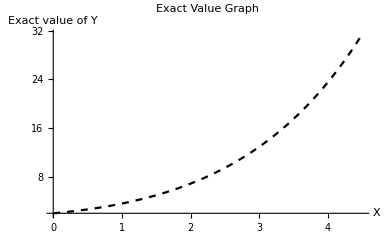

```mathematica
P1=Plot[-2+4 ⅇ^(x/2)-x//N ,{x, 0,4.5},PlotRange->Full,PlotStyle->{Dashed,Black},AxesLabel->{"X","Exact value of Y"}, PlotLabel->"Exact Value Graph",LabelStyle->{Brown,19,Bold,Italic}]
```

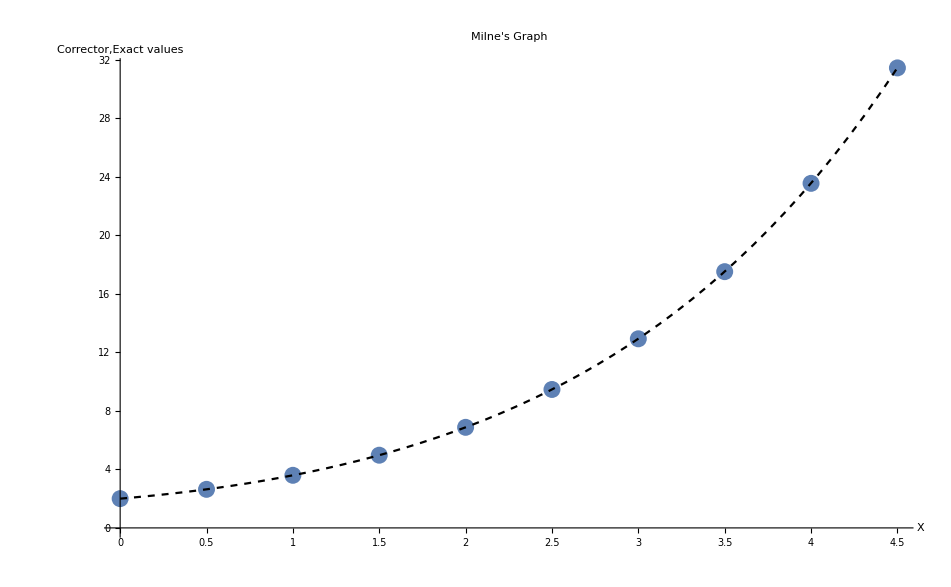

```mathematica
m1=Show[ListPlot[Corrector], P1,PlotLabel->"Milne's Graph",AxesLabel->{"X","Corrector,Exact values"},LabelStyle->{Brown,20,Bold},Ticks->{{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5},Automatic}]
```